# Tensor Network

QuantumCircuitOperator[…]["TensorNetwork"] | returns the tensor network of a circuit
TensorNetworkIndexGraph[…] | transforms a tensor network into a new graph with indices as vertices
TensorNetworkFreeIndices[…] | returns free indices in a tensor network index graph
ContractTensorNetwork[…] | contracts indices in a tensor network

Create a quantum circuit:

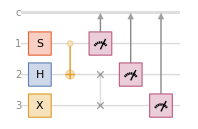

```mathematica
circuit=QuantumCircuitOperator[{"S","H"->2,"X"->3,"CNOT","SWAP"->{2,3},{1},{2},{3}}];
circuit["Diagram"]
```

In the Wolfram Quantum Framework, measurement outcomes are recorded in an ancillary quantum register (serving as a detector), so the complete circuit diagram includes both the system and this detector subsystem.

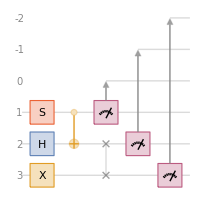

```mathematica
circuit["Diagram","ShowExtraQudits"->True]
```

The first measurement result is stored in wire index 0, with subsequent results assigned to decreasing (negative) wire indices.

Returns the tensor network representation corresponding to the given quantum circuit:

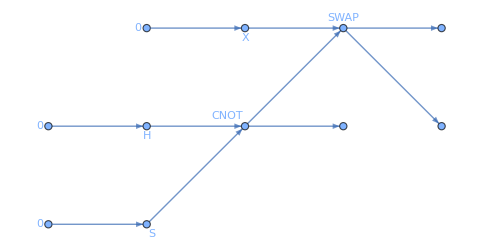

```mathematica
net=circuit["TensorNetwork",GraphLayout -> {"LayeredDigraphEmbedding", "Orientation" -> Left}]
```

The tensor network is a graph annotated with tensors and contraction indices.

```mathematica
GraphQ[net]&&TensorNetworkQ[net]
```

True

For a graph to be a tensor network, two main conditions must be met, which is what TensorNetworkQ does. First, every vertex in the graph must have properly formatted indices consisting only of Subscript or Superscript expressions, and each vertex cannot contain any duplicate indices - all indices at any single vertex must be unique from each other.

Second, the tensor rank compatibility condition must be satisfied. This can happen in two ways: either each vertex's tensor rank must exactly match the number of indices assigned to that vertex, and when counting all index occurrences throughout the entire graph, every distinct index must appear exactly twice across all vertices (ensuring proper pairing for tensor contraction), or alternatively, all tensors in the network must have rank zero representing scalar tensors with no indices.

Lists all annotation keys available for the tensor network:

```mathematica
AnnotationKeys[{net,0}]
```

{Index,Tensor,VertexCoordinates,VertexLabels,VertexShape,VertexShapeFunction,VertexSize,VertexStyle}

Let’s look at tensor, vertex labels, and corresponding indexes in the tensor network:

```mathematica
list=Developer`FromPackedArray@VertexList[net];
TableForm[Transpose[Prepend[AnnotationValue[{net,list},#]&/@{"Tensor","Index"},Sort@AnnotationValue[net,VertexLabels]]],TableDepth->2,TableHeadings->{None,(Style[#1,Bold]&)/@{"Vertex index ->\n Vertex label","Tensor","Leg indices"}}]
```

Vertex index ->
 Vertex label | Tensor | Leg indices
-2→0 | SparseArray[…] | {(-2)^1}
-1→0 | SparseArray[…] | {(-1)^2}
0→0 | SparseArray[…] | {0^3}
1→S | SparseArray[…] | {1^1,1_1}
2→H | SparseArray[…] | {2^2,2_2}
3→X | SparseArray[…] | {3^3,3_3}
4→CNOT | SparseArray[…] | {4^1,4^2,4_1,4_2}
5→SWAP | SparseArray[…] | {5^2,5^3,5_2,5_3}
6→None | SparseArray[…] | {6^0,6^1,6_1}
7→None | SparseArray[…] | {7^-1,7^2,7_2}
8→None | SparseArray[…] | {8^-2,8^3,8_3}

Tensors in the tensor network are mixed type, meaning they consist of so-called “contravariant” (upper) indices and “covariant” (lower) indices. For example, the 2nd measurement (7th vertex), acts on qubit-2 (denoted by contravariant and covariant indices 2) and its result is saved on wire, denoted by the index “-1”.

Vertices correspond to circuit’s operators/gate indices, in addition to “Initial” tensor with index 0 (for the initial state):

```mathematica
VertexList[net]
```

{-2,-1,0,1,2,3,4,5,6,7,8}

```mathematica
Length@circuit["Flatten"]["Operators"]
```

8

```mathematica
%==Max[%%]
```

True

Note that each edge represents (i.e., is tagged by) a contraction:

```mathematica
EdgeList[net]
```

{-21{(-2)^1,1_1},-12{(-1)^2,2_2},03{0^3,3_3},14{1^1,4_1},24{2^2,4_2},45{4^2,5_2},35{3^3,5_3},46{4^1,6_1},57{5^2,7_2},58{5^3,8_3}}

Corresponding contraction:

```mathematica
EdgeTags[net]
```

{{(-2)^1,1_1},{(-1)^2,2_2},{0^3,3_3},{1^1,4_1},{2^2,4_2},{4^2,5_2},{3^3,5_3},{4^1,6_1},{5^2,7_2},{5^3,8_3}}

Perform the contraction:

```mathematica
finalTensor=ContractTensorNetwork[net]
```

SparseArray[…]

Confirm that the result is the same as default circuit application:

```mathematica
circuit[]["Tensor"]==finalTensor
```

True

Another tensor network representation uses indices as graph vertices with tensors as cliques:

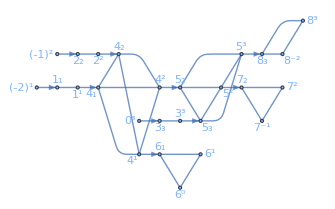

```mathematica
indexNet=TensorNetworkIndexGraph[net,GraphLayout -> {"LayeredDigraphEmbedding", "Orientation" -> Left}]
```

In the above graph, the directed edges imply tensor contraction; also tensors are cliques in above graph:

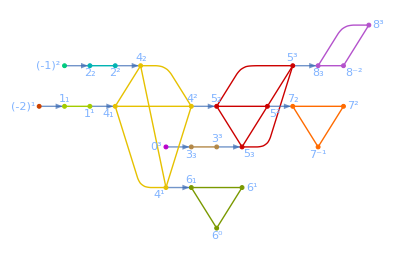

```mathematica
HighlightGraph[indexNet,Subgraph[indexNet,#]&/@FindClique[indexNet,Infinity,All]]
```

Free indices are the ones that left after contraction:

```mathematica
TensorNetworkFreeIndices[net]
```

{8^-2,7^-1,6^0,6^1,7^2,8^3}

Highlight free indices:

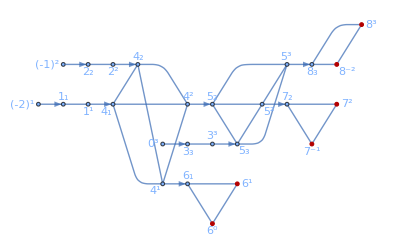

```mathematica
HighlightGraph[indexNet,TensorNetworkFreeIndices[net]]
```

Free indices can be extracted as vertices with zero in- and out- degree:

```mathematica
Pick[VertexList[indexNet],VertexInDegree[indexNet]+VertexOutDegree[indexNet],0]
```

{6^0,6^1,7^-1,7^2,8^-2,8^3}

```mathematica
ContainsExactly[TensorNetworkFreeIndices[net],TensorNetworkFreeIndices[net]]
```

True

### Contraction and Einstein Summation

Many useful information of a tensor network can be extracted using TensorNetworkData:

```mathematica
TensorNetworkData[net]//Dataset
```

Also, one can get the useful data using graph functionalities, too:

```mathematica
indices=AnnotationValue[{net,list},"Index"]/.Rule@@@EdgeTags[net]
out=TensorNetworkFreeIndices[net]
tensors=AnnotationValue[{net,list},"Tensor"];
```

{{1_1},{2_2},{3_3},{4_1,1_1},{4_2,2_2},{5_3,3_3},{6_1,5_2,4_1,4_2},{7_2,8_3,5_2,5_3},{6^0,6^1,6_1},{7^-1,7^2,7_2},{8^-2,8^3,8_3}}

{8^-2,7^-1,6^0,6^1,7^2,8^3}

Show ContractTensorNetwork is the same as EinsteinSummation:

```mathematica
ContractTensorNetwork[net]===ActivateTensor@EinsteinSummation[indices->out,tensors]
```

True

One can compare the performance, on how the relevant computation is done

Perform the contraction in the order of network’s EdgeList:

```mathematica
ContractTensorNetwork[net,Method->"Naive"];//RepeatedTiming
```

{0.00928845,Null}

Optimize the order for contraction, using EinsteinSummation and symbolic tensors package:

```mathematica
ContractTensorNetwork[net];//RepeatedTiming
```

{0.00183096,Null}

### Initial state different from ground state

Note that the initial tensor in the tensor network we studied here was a registered state. Additionally, one can start from any initial state.

Generate a random state:

```mathematica
ψ0=QuantumState[{"RandomPure",3}];
```

Initialize the tensor network from above state:

```mathematica
net2=QuantumCircuitOperator[{ψ0,circuit}]["TensorNetwork"];
```

See supplement info, for package-scoped symbols.

Show the tensor contraction is the same as transformation of state by the circuit:

```mathematica
ContractTensorNetwork[net2]==circuit[ψ0]["Tensor"]
```

True

## Supplement info

### FromTensorNetwork

Any directed graph can be turned into a tensor network, even if the graph is not annotated.

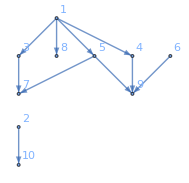

```mathematica
SeedRandom[1];
graph=DirectedGraph[RandomGraph[{10,10}],"Acyclic",VertexLabels->v_:>HoldForm[v]]
```

Convert the graph into a tensor network such that tensors for each vertex is randomly generated in the dimension {2,2,…} where the overall length of dimensions is determined by the tensor rank (overall legs/edges):

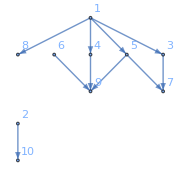

```mathematica
qcTN=GraphTensorNetwork@graph
```

Get the tensor network data:

```mathematica
TensorNetworkData@qcTN
```

<|Tensors→{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]},Dimensions→{{2},{2},{2},{2,2,2,2},{2},{2,2,2},{2,2},{2,2,2},{2,2},{2,2}},Indices→{{6^1},{2^2},{10_2},{1^2,1^3,1^4,1^5},{8_2},{5^2,5^3,5_3},{4^4,4_4},{9_1,9_2,9_4},{3^5,3_5},{7_3,7_5}},Vertices→{6,2,10,1,8,5,4,9,3,7},FreeIndices→{},Bonds→{6→{9,2},2→{10,2},1→{3,2},1→{4,2},1→{5,2},1→{8,2},5→{7,2},5→{9,2},4→{9,2},3→{7,2}},Contractions→{{{6^1,9_1}},{{2^2,10_2}},{{2^2,10_2}},{{1^2,8_2},{1^3,5_3},{1^4,4_4},{1^5,3_5}},{{1^2,8_2}},{{5^2,9_2},{5^3,7_3},{1^3,5_3}},{{4^4,9_4},{1^4,4_4}},{{6^1,9_1},{5^2,9_2},{4^4,9_4}},{{3^5,7_5},{1^5,3_5}},{{5^3,7_3},{3^5,7_5}}},ContractionIndices→{{6^1},{2^2},{2^2},{1^2,1^3,1^4,1^5},{1^2},{5^2,5^3,1^3},{4^4,1^4},{6^1,5^2,4^4},{3^5,1^5},{5^3,3^5}}|>

One can assign symbolic tensor into vertices too:

```mathematica
qcTNSymbolic=GraphTensorNetwork[graph,Method->"Symbolic"];
TensorNetworkData@qcTNSymbolic
```

<|Tensors→{612,212,1012,142222,812,53222,4222,93222,3222,7222},Dimensions→{{2},{2},{2},{2,2,2,2},{2},{2,2,2},{2,2},{2,2,2},{2,2},{2,2}},Indices→{{6^1},{2^2},{10_2},{1^2,1^3,1^4,1^5},{8_2},{5^2,5^3,5_3},{4^4,4_4},{9_1,9_2,9_4},{3^5,3_5},{7_3,7_5}},Vertices→{6,2,10,1,8,5,4,9,3,7},FreeIndices→{},Bonds→{6→{9,2},2→{10,2},1→{3,2},1→{4,2},1→{5,2},1→{8,2},5→{7,2},5→{9,2},4→{9,2},3→{7,2}},Contractions→{{{6^1,9_1}},{{2^2,10_2}},{{2^2,10_2}},{{1^2,8_2},{1^3,5_3},{1^4,4_4},{1^5,3_5}},{{1^2,8_2}},{{5^2,9_2},{5^3,7_3},{1^3,5_3}},{{4^4,9_4},{1^4,4_4}},{{6^1,9_1},{5^2,9_2},{4^4,9_4}},{{3^5,7_5},{1^5,3_5}},{{5^3,7_3},{3^5,7_5}}},ContractionIndices→{{6^1},{2^2},{2^2},{1^2,1^3,1^4,1^5},{1^2},{5^2,5^3,1^3},{4^4,1^4},{6^1,5^2,4^4},{3^5,1^5},{5^3,3^5}}|>

### Package-scoped symbols

In the Wolfram quantum framework, there are some package-scoped symbols that live in Wolfram`QuantumFramework`PackageScope` context.

```mathematica
?Wolfram`QuantumFramework`PackageScope`$*
```

Related Guides

Related Tech Notes

## Metadata

### Categorization

Tech Note

Wolfram/QuantumFramework

Wolfram`QuantumFrameworkLoader`

Wolfram/QuantumFramework/tutorial/TensorNetwork

### Keywords